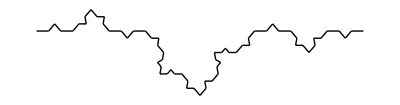

```mathematica
(*
Stwórz procedurę rysującą płatek Kocha do N-tego pokolenia,w którym co drugi segment jest odwrócony.
*)
Clear[n,Snowflake,start,finish,doline]
Snowflake[n_Integer?NonNegative]:=(
lista = Range[n];
Show[Graphics[Fold[(#1/.Line[{start_,finish_}]:>doline[start,finish, #2])&,{Line[{{0,0},{1,0}}]},lista]],
AspectRatio->Automatic,PlotRange->All])
doline[start_,finish_, segment_]:=Module[{vec,Normal},vec=finish-start;
normal=Reverse[vec] {-1,1} Sqrt[2.5]/8;
If [Mod[$ModuleNumber,2]== 0, normal=normal, normal =  -normal];
znak =1;
(* poniższy fragment odwraca co drugie pokolenie sposób malowania lini, raz góra raz dół
If[Mod[segment,2]==0,znak = 1,znak =-1];
*)
{Line[{start,start+vec/3}],Line[{start+vec/3,start+vec/2+normal*znak}],Line[{start+vec/2+normal*znak,start+2 vec/3}],Line[{start+2 vec/3,finish}]}];
Snowflake[3]
```